```mathematica
SetDirectory[NotebookDirectory[]];
<<rotationtools.wl
```

```mathematica
(*Writing modules to create pure translation and pure rotation quaternions*)
```

```mathematica
(*Quaternion Modules*)
```

```mathematica
quat[θ_,k_ ]:=Module[{},
Return[{Cos[θ/2], Sin[θ/2]{k[[1]], k[[2]], k[[3]]}}];
]
```

```mathematica
qmult[q1_, q2_]:=Module[{},
Return[{q1[[1]]*q2[[1]]-q1[[2]].q2[[2]], q1[[1]]*q2[[2]]+q1[[2]]*q2[[1]]+Cross[q1[[2]], q2[[2]]]}];
]
```

```mathematica
cquat[q_]:=Module[{},
Return[{q[[1]], -q[[2]]}];
];
```

```mathematica
(*Dual Quaternion Modules*)
```

```mathematica
(*Module for unit dual quaternions, given a unit rotation θ, axis, k and translation t. This module is to produce a dual quaternion representing a translation followed by rotation*)
```

```mathematica
unitdq[ t_, θ_, k_]:=Module[{qrot},
qrot = quat[θ, k];
Return[{qrot, qmult[{0,t}, qrot]/2}];
]
```

```mathematica
cdualq[dq1_]:=Module[{},
Return[{cquat[dq1[[1]]], cquat[dq1[[2]]]}];
];
```

```mathematica
dqmult[dq1_, dq2_]:=Module[{},
Return[ {qmult[dq1[[1]], dq2[[1]]], qmult[dq1[[2]], dq2[[1]]]+qmult[dq1[[1]], dq2[[2]]]}];
]
```

```mathematica
(*Test cases*)
```

```mathematica
qt = quat[0, {2, 0, 0}];
q1 = quat[ π/3, {1, 0, 0}];
q2 = quat[π/6, {1, 0, 1}];
```

```mathematica
N[q2];
N[cquat[q2]];
```

```mathematica
qmult[q1, q2];
```

```mathematica
dq1 = unitdq[{1,1,1}, π/3, {0,0,1}];
dq2 = unitdq[{1,0,1}, π/6, {1,0,1}];
```

```mathematica
N[dqmult[dq1, dq2]];
```

```mathematica
N[dq1];
N[cdualq[dq1]];
```

```mathematica
(*Testing the Hamiltonian Operator for given quaternion or a dual quaternion*)
```

```mathematica
Hp[q_] := Module[{a0, a1, a2, a3},
a0 = q[[1]];a1 = q[[2]][[1]];a2 = q[[2]][[2]];a3 = q[[2]][[3]];
Return[{{a0, -a1, -a2, -a3},{a1, a0, -a3, a2},{a2, a3, a0, -a1},{a3, -a2, a1, a0}}];
]
```

```mathematica
Hn[q_] := Module[{a0, a1, a2, a3},
a0 = q[[1]];a1 = q[[2]][[1]];a2 = q[[2]][[2]];a3 = q[[2]][[3]];
Return[{{a0, -a1, -a2, -a3},{a1, a0, a3, -a2},{a2, -a3, a0, a1},{a3, a2, -a1, a0}}];
]
```

```mathematica
dHp[dq1_]:=Module[{},
Return[N[ArrayFlatten[{{Hp[dq1[[1]]], ConstantArray[0,{4,4}]},{Hp[dq1[[2]]], Hp[dq1[[1]]]}}]]];
]
```

```mathematica
dHn[dq1_]:=Module[{},
Return[N[ArrayFlatten[{{Hn[dq2[[1]]], ConstantArray[0,{4,4}]},{Hn[dq2[[2]]], Hn[dq2[[1]]]}}]]];
]
```

```mathematica
(*Verification of the properties of the Hamiltonian Operator for quaternions and dual quaternions*)
```

```mathematica
Chop[Flatten[N[qmult[q1,q2]]]-N[Hp[q1].Flatten[q2]]]
Chop[Flatten[N[qmult[q1,q2]]]-N[Hn[q2].Flatten[q1]]]
```

{0,0,0,0}

{0,0,0,0}

```mathematica
Chop[Flatten[N[dqmult[dq1, dq2]]]-dHp[dq1].Flatten[dq2]]
Chop[Flatten[N[dqmult[dq1, dq2]]]-dHn[dq2].Flatten[dq1]]
```

{0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0}

```mathematica
(*Now define the FK of the interms of the six angles at each of the joint*)
```

```mathematica
(*Using the DH parameters of PUMA 560 robot*)
```

```mathematica
pq1 = unitdq[{0,0,0},θ1, {0,0,1}];
pq2 = unitdq[{0,0,0},-π/2, {1,0,0}];
pq3 = unitdq[{0,0,0},θ2, {0,0,1}];
pq4 =unitdq[{a2,0,0},0,{1,0,0}];
pq5 =unitdq[{0,0,d3},θ3,{0,0,1}];
pq6 = unitdq[{0, 0, 0}, -π/2, {1, 0, 0}];
pq7 = unitdq[{a3,0,0},0,{1,0,0}];
pq8 = unitdq[{0,0,d4},θ4,{0,0,1}];
pq9 = unitdq[{0,0,0},π/2,{1,0,0}];
pq10 = unitdq[{0,0,0},θ5,{0,0,1}];
pq11 = unitdq[{0,0,0},-π/2,{1,0,0}];
pq12 = unitdq[{0,0,0},θ6,{0,0,1}];
```

```mathematica
(*Now computing the fk quaternion*)
```

```mathematica
fkq = Simplify[dqmult[dqmult[dqmult[dqmult[dqmult[dqmult[dqmult[dqmult[dqmult[dqmult[dqmult[pq1, pq2], pq3], pq4], pq5], pq6], pq7], pq8], pq9], pq10], pq11], pq12]];
```

```mathematica
fkqp= fkq/.params;
```

```mathematica
(*Validation of the FK*)
```

```mathematica
(*sampleangles3 = {θ1->3π/4, θ2->π/6, θ3->π/3, θ4->3π/4, θ5->-π/3, θ6->2π/3};*)
```

```mathematica
(*Produces great change*)
```

```mathematica
(*sampleangles3 = {θ1->3π/4, θ2->π/4, θ3->π/3, θ4->π/6, θ5->-π/4, θ6->2π/3};*)
```

```mathematica
(*Details of the PUMA 560 robot*)
```

```mathematica
params = {a2->0.4318 , d3->0.125, a3->0.019, d4->0.432};
sampleangles = {θ1->π/4, θ2->π/3, θ3->3π/4, θ4->π/6, θ5->-π/4, θ6->2π/3};
sampleangles2 = {θ1->π/2, θ2->π/6, θ3->π/3, θ4->3π/4, θ5->-π/3, θ6->2π/3};
sampleangles3 = {θ1->π/2, θ2->π/4, θ3->π/3, θ4->π/6, θ5->-π/4, θ6->2π/3};
```

```mathematica
fkqs = N[fkq/.params/.sampleangles]
fkqs2 = N[fkq/.params/.sampleangles2]
fkqs3 = N[fkq/.params/.sampleangles3]
2*(logdq[fkqs]-logdq[fkqs3])[[2]]
```

{{-0.954287,{-0.277118,0.0495229,-0.100444}},{0.0128805,{-0.0788202,-0.146687,0.0227634}}}

{{0.135299,{-0.29516,0.326641,-0.887626}},{-0.113218,{0.0556712,-0.0247371,-0.044873}}}

{{-0.401802,{-0.790675,0.281211,-0.366481}},{-0.0718083,{0.076318,0.0843347,-0.0212132}}}

{0.25536,0.424006,0.260119}

```mathematica
(*Finding the homogeneous transformation matrix from the dual quaternion*)
```

```mathematica
halfsin = Norm[fkqs[[1]][[2]]];
θs = 2*ArcTan[fkqs[[1]][[1]], Norm[fkqs[[1]][[2]]]];
kvecs = fkqs[[1]][[2]]/halfsin;
```

```mathematica
halfsin2 = Norm[fkqs2[[1]][[2]]];
θs2 = 2*ArcTan[fkqs2[[1]][[1]], Norm[fkqs2[[1]][[2]]]];
kvecs2 = fkqs2[[1]][[2]]/halfsin2;
```

```mathematica
Amats = vec2SkewMat[Tan[θs/2]*kvecs];
Amats2 = vec2SkewMat[Tan[θs2/2]*kvecs2];
```

```mathematica
(*Verifications with values given in Ghosal et. al.*)
```

```mathematica
Rmats = Inverse[IdentityMatrix[3]-Amats].(IdentityMatrix[3]+Amats)//MatrixForm
```

(0.974917 | -0.219152 | -0.0388486
0.164257 | 0.826234 | -0.538849
0.150188 | 0.518952 | 0.841506)

```mathematica
Rmats2 = Inverse[IdentityMatrix[3]-Amats2].(IdentityMatrix[3]+Amats2)//MatrixForm
```

(-0.789149 | 0.0473672 | 0.612372
-0.433013 | -0.75 | -0.5
0.435596 | -0.65974 | 0.612372)

```mathematica
tempt = {0, {tx, ty, tz}};
```

```mathematica
temptsol = Solve[((qmult[tempt, fkqs[[1]]] - 2*fkqs[[2]])[[2]])==0 ,{tx, ty, tz}][[1]]
```

{tx→0.13036,ty→0.307137,tz→0.0482477}

```mathematica
temptsol2 = Solve[((qmult[tempt, fkqs2[[1]]] - 2*fkqs2[[2]])[[2]])==0 ,{tx, ty, tz}][[1]]
```

{tx→-0.125,ty→-0.0580502,tz→-0.2349}

```mathematica
(*Residues*)
```

```mathematica
(qmult[tempt, fkqs[[1]]]-2*fkqs[[2]])/.temptsol
```

{5.89806×10^-17,{-6.93889×10^-18,5.55112×10^-17,1.38778×10^-17}}

```mathematica
(qmult[tempt, fkqs2[[1]]]-2*fkqs2[[2]])/.temptsol2
```

{-2.498×10^-16,{0.,1.38778×10^-17,6.93889×10^-18}}

```mathematica
(*Now we have an FK quaternion. We have to formulate the Jacobian in q terms. For which we flatten the quaternion and take the derivative wrt all the angles*)
```

```mathematica
flatfkq = Flatten[fkq];
```

```mathematica
(*Now computing the Jacobian, wrt θ*)
```

```mathematica
θsym = {θ1, θ2, θ3, θ4, θ5, θ6};
```

```mathematica
Jquatθ = D[flatfkq, {θsym}];
```

```mathematica
Jquatθs = N[Jquatθ/.params/.sampleangles];
```

```mathematica
(* Now we can proceed to do a kinematic control, assuming (wrongly) that the error is qe = qd-qc *)
```

```mathematica
(*Since the computation of pseudo inverse is tricky and expensive we keep it aside and go with J^T*)
```

```mathematica
(*Using Transpose[Jquatθ]*)
```

```mathematica
qetemp = MatrixExp[Jquatθs.Transpose[Jquatθs]].ConstantArray[0.1,{8,1}]
```

{{0.0926826},{0.0969273},{0.137584},{0.196529},{0.094762},{0.107543},{0.102368},{0.0985833}}

```mathematica
Transpose[Jquatθs].qetemp
```

{{-0.107172},{-0.00513511},{-0.0373443},{-0.116087},{-0.0158783},{-0.0719511}}

```mathematica
(*Then do an Euler step to find the θ at the current instant*)
```

```mathematica
(*Desired quaternion is*)
```

```mathematica
qd2 = N[fkq/.params/.sampleangles3]
```

{{-0.401802,{-0.790675,0.281211,-0.366481}},{-0.0718083,{0.076318,0.0843347,-0.0212132}}}

```mathematica
qd = N[fkq/.params/.sampleangles2]
```

{{0.135299,{-0.29516,0.326641,-0.887626}},{-0.113218,{0.0556712,-0.0247371,-0.044873}}}

```mathematica
(*Initial quaternion is*)
```

```mathematica
qi = N[fkq/.params/.sampleangles]
```

{{-0.954287,{-0.277118,0.0495229,-0.100444}},{0.0128805,{-0.0788202,-0.146687,0.0227634}}}

```mathematica
(*Error dynamics is*)
```

```mathematica
Jqtp = Jquatθ/.params;
```

```mathematica
cJqtp = Compile[{{θ1, _Real}, {θ2, _Real}, {θ3, _Real}, {θ4, _Real}, {θ5, _Real},{θ6, _Real}}, Evaluate[Jqtp]];
```

```mathematica
cJqtps=cJqtp[(θsym/.sampleangles)[[1]], (θsym/.sampleangles)[[2]], (θsym/.sampleangles)[[3]], (θsym/.sampleangles)[[4]], (θsym/.sampleangles)[[5]], (θsym/.sampleangles)[[6]]]
```

{{0.0502218,-0.115485,-0.115485,0.069337,-0.132376,0.0502218},{-0.0247614,0.301879,0.301879,-0.120432,0.438329,0.0247614},{-0.138559,-0.372904,-0.372904,-0.21197,-0.195078,0.138559},{-0.477144,0.080467,0.080467,-0.430996,-0.0478354,-0.477144},{-0.0113817,0.0239944,0.0649279,0.050799,0.0025415,-0.0113817},{0.0733433,0.00349412,-0.141299,-0.0565544,-0.0112683,-0.0733433},{-0.0394101,0.012602,-0.130201,0.035835,-0.0066367,0.0394101},{0.00644026,0.0797287,0.019899,0.00635106,-0.0832222,0.00644026}}

```mathematica
Bmat[z_/;VectorQ[z, NumericQ]] := Module[{k, Bmattemp, Jqtpval, b2temp},
k = 850;
Jqtpval = cJqtp[z[[1]], z[[2]], z[[3]], z[[4]], z[[5]], z[[6]]];
Bmattemp = N[ArrayFlatten[{{ConstantArray[0,{14,6}],ArrayFlatten[{{Transpose[Jqtpval]*k}, {-Jqtpval.Transpose[Jqtpval]*k}}]}}]];
b2temp = Bmattemp.z;
Return[b2temp];
]
```

```mathematica
(*Initial error (wrongly) *)
```

```mathematica
(*CHANGING qd!!!*)
```

```mathematica
qei = qd2-qi
```

{{0.552486,{-0.513557,0.231688,-0.266038}},{-0.0846888,{0.155138,0.231021,-0.0439765}}}

```mathematica
motionsim = NDSolve[{Bmat[z[t]]== z'[t],z[0]==Join[θsym/.sampleangles,Flatten[qei]]},z,{t, 0, 15}][[1]];
```

```mathematica
(*Final value reached vs desired value*)
```

```mathematica
thf = Flatten[z[t]/.motionsim/.t->15][[1;;6]]
thd = N[Flatten[θsym/.sampleangles3]]
```

{1.5708,0.785399,1.0472,0.5236,-0.785399,2.09439}

{1.5708,0.785398,1.0472,0.523599,-0.785398,2.0944}

```mathematica
(*Error in the quaternions*)
```

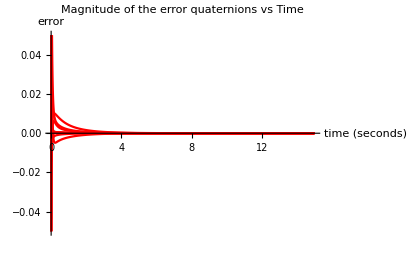

```mathematica
Plot[(z[t]/.motionsim)[[7;;14]], {t, 0, 15}, PlotStyle->Red, PlotRange->{{0,15},{-0.05,0.05}},AxesLabel->{"time (seconds) ", "error"}, PlotLabel->"Magnitude of the error quaternions vs Time"]
```

```mathematica
(*Angles converging*)
```

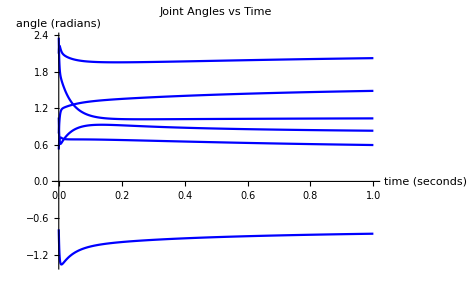

```mathematica
Plot[(z[t]/.motionsim)[[1;;6]], {t, 0, 01}, PlotStyle->Blue, AxesLabel-> {"time (seconds)", "angle (radians)"}, PlotLabel->"Joint Angles vs Time"]
```

```mathematica
(* Bringing the errors to within 2% *)
```

```mathematica
(Abs[thf-thd]/thd)*100
```

{0.0000662249,0.0000762141,0.0000165961,0.000181129,-0.00010986,0.0000443558}

```mathematica
(*Peak overshoot among all the other peaks*)
```

```mathematica
Table[Max[Abs[Table[((z[t]/.motionsim/.t->tval)[[j]])-thd[[j]],{tval, 0,10, 0.01 }]]], {j, 1, 6}]
```

{0.785398,0.261799,1.309,0.185546,0.573214,0.142098}

```mathematica
(*Max steady state error*)
```

```mathematica
Max[Abs[thf-thd]]
```

1.04026×10^-6

```mathematica
(*Plotting the translation of the end-effector*)
```

```mathematica
zang = Table[(z[t]/.motionsim/.t->tval)[[1;;6]],{tval, 0, 10, 0.01}];
```

```mathematica
zθrule = Table[Inner[Rule, θsym, zang[[i]], List],{i,1001}];
```

```mathematica
zdist = Table[2*(logdq[fkqp/.zθrule[[i]]])[[2]], {i, 1001}];
```

```mathematica
ListPointPlot3D[zdist]
```

-Graphics3D-

```mathematica
(*We observe the discontinuities in the angles at the beginning*)
```

```mathematica
zang = Table[(z[t]/.motionsim/.t->tval)[[1;;6]],{tval, 0, 10, 0.01}];
```

```mathematica
zang//Dimensions
```

{10001,6}

```mathematica
zθrule = Table[Inner[Rule, θsym, zang[[i]], List],{i,1001}];
```

```mathematica
zeefang = Table[2*(logdq[fkqp/.zθrule[[i]]])[[1]], {i, 1001}];
```

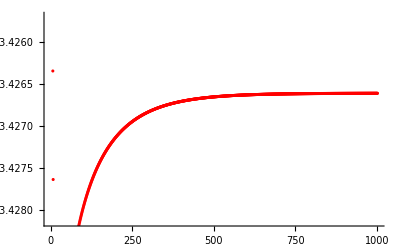

```mathematica
ListPlot[Flatten[zeefang[[;;,1;;1]]], PlotStyle->{Red}]
```

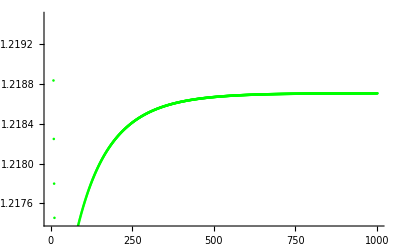

```mathematica
ListPlot[Flatten[zeefang[[;;,2;;2]]], PlotStyle->{Green}]
```

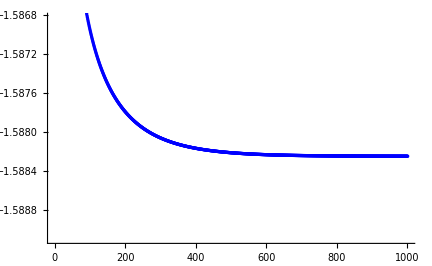

```mathematica
ListPlot[Flatten[zeefang[[;;,3;;3]]], PlotStyle->{Blue}]
```

```mathematica
(*Increasing the resolution at the beginning*)
```

```mathematica
zang = Table[(z[t]/.motionsim/.t->tval)[[1;;6]],{tval, 0, 1, 0.0001}];
```

```mathematica
zang//Dimensions
```

{10001,6}

```mathematica
zθrule = Table[Inner[Rule, θsym, zang[[i]], List],{i,10001}];
```

```mathematica
zeefang = Table[2*(logdq[fkqp/.zθrule[[i]]])[[1]], {i, 10001}];
```

```mathematica
zeefang//Dimensions
```

{10001,3}

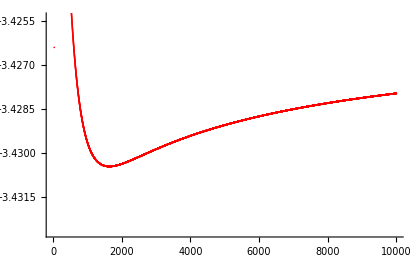

```mathematica
ListPlot[Flatten[zeefang[[;;,1;;1 ]]], PlotStyle->{Red}]
```

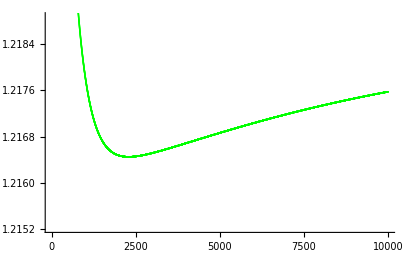

```mathematica
ListPlot[Flatten[zeefang[[;;,2;;2]]], PlotStyle->{Green}]
```

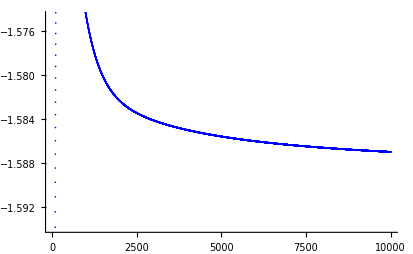

```mathematica
ListPlot[Flatten[zeefang[[;;,3;;3]]], PlotStyle->{Blue}]
```

```mathematica
(*Tuning the value of k for settling time and peak overshoot*)
```

```mathematica
(*This integration gives the angles at each instant of time and also the plot of error asymptotically decreasing with time*)
```

```mathematica
(*Error measure needs to be changed and explanation on why this worked in this paper needs to be given*)
```

```mathematica
(*Cooperative task-space control with two PUMA 560's*)
```

```mathematica
(*Primitive-1: Relative dual position control, so the controlled variable is qr. So we need the Jacbian for this control*)
```

```mathematica
(*We need fk of two robots in the cooperative workspace*)
```

```mathematica
αsym = {θ1, θ2, θ3, θ4, θ5, θ6}/.{θ1->α1, θ2->α2, θ3->α3, θ4->α4, θ5->α5, θ6->α6};
βsym = {θ1, θ2, θ3, θ4, θ5, θ6}/.{θ1->β1, θ2->β2, θ3->β3, θ4->β4, θ5->β5, θ6->β6};
```

```mathematica
fkq1 = fkq/.{θ1->α1, θ2->α2, θ3->α3, θ4->α4, θ5->α5, θ6->α6}/.params;
fkq2 = fkq/.{θ1->β1, θ2->β2, θ3->β3, θ4->β4, θ5->β5, θ6->β6}/.params;
```

```mathematica
Jq1 = D[Flatten[fkq1], {αsym}];
```

```mathematica
cq2 = cdualq[fkq2];
```

```mathematica
Jcq2 = D[Flatten[cq2], {βsym}];
```

```mathematica
sampleα = sampleangles/.{θ1->α1, θ2->α2, θ3->α3, θ4->α4, θ5->α5, θ6->α6};
sampleβ = sampleangles3/.{θ1->β1, θ2->β2, θ3->β3, θ4->β4, θ5->β5, θ6->β6};
```

```mathematica
Jqr = ArrayFlatten[{{dHn[fkq1].Jcq2, dHp[cq2].Jq1}}];
```

```mathematica
Jqr/.sampleα/.sampleβ//MatrixForm
```

(0.213431 | -0.307415 | -0.307415 | 0.262839 | -0.341495 | 0.202361 | 0.25 | -0.25 | -0.25 | 0.306186 | -0.304895 | 0.196642
0.151515 | -0.303706 | -0.303706 | -0.0406405 | -0.346892 | -0.0240863 | 0.0956205 | 0.0205267 | 0.0205267 | 0.171856 | -0.118186 | -0.0522561
0.440198 | 0.228228 | 0.228228 | -0.023707 | -0.033388 | -0.380418 | 0.421856 | 0.16238 | 0.16238 | 0.353849 | 0.295297 | 0.382232
0.0668058 | 0.167087 | 0.167087 | 0.442096 | 0.16935 | 0.283723 | 0.0198648 | -0.400888 | -0.400888 | -0.0388164 | -0.236371 | 0.25
-0.107821 | 0.121282 | 0.120826 | -0.21919 | 0.102946 | -0.100754 | -0.056576 | -0.0737312 | 0.0737312 | 0.019948 | 0.0559373 | 0.0945698
0.379694 | -0.0632737 | 0.00823055 | 0.0833384 | -0.227318 | -0.129724 | 0.0503564 | 0.0122833 | 0.147782 | 0.0987742 | -0.00171129 | 0.0295
-0.0671486 | 0.247529 | 0.425442 | 0.297753 | 0.247582 | 0.193768 | 0.0226068 | -0.0156135 | -0.00202462 | -0.0565058 | 0.110188 | -0.0816226
-0.0742228 | -0.229976 | -0.343859 | 0.153943 | -0.209228 | 0.320654 | -0.0104671 | 0.0402846 | -0.0392331 | 0.0795589 | 0.066359 | 0.056576)

```mathematica
(*Primitive-2: Relative cartesian position control, so the controlled variable is tr. So we need the Jacbian for this control*)
```

```mathematica
dqr = dqmult[cdualq[fkq2], fkq1];
```

```mathematica
qr = dqr[[1]];
qr0 = dqr[[2]];
```

```mathematica
fullspace = Join[βsym, αsym];
```

```mathematica
Jqr0 = D[Flatten[qr0],{fullspace}];
```

```mathematica
Jcqr = D[Flatten[cquat[qr]],{fullspace}];
```

```mathematica
Jtr = 2*(Hn[cquat[qr]].Jqr0+Hp[qr0].Jcqr);
```

```mathematica
Chop[Jtr/.sampleα/.sampleβ]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.118115 | 0.107936 | -0.0921552 | -0.141167 | 0.0781114 | -0.334933 | -0.118115 | -0.221536 | 0.166732 | 0 | 0 | 0
0.0681416 | 0.0786972 | 0.106079 | -0.353766 | 0.135293 | -0.422189 | -0.0681416 | -0.168463 | -0.352206 | 0 | 0 | 0
0.30452 | -0.0104609 | 0.3712 | 0.376953 | -0.078966 | 0 | -0.30452 | 0.143429 | 0.187446 | 0 | 0 | 0)

```mathematica
(*Now we have both the primitives required for pouring water into a glass. All we need is the required initial and final configurations*)
```

```mathematica
(*We have already assumed that both the arms start from the same point. This is an ok assumption as we are dealing with robots with two arms, hypotheticall originating from the same point in the body. Also we are dealing with virtual robots and hence collisions are ignored.*)
```

```mathematica
(*For the task of pouring water into a glass, we have the initial configuration, we need to decide on a final configuration to achieve this*)
```

```mathematica
(*Finding the initial relative distance between the two configurations*)
```

```mathematica
dqrs = N[dqr/.sampleα/.sampleβ]
```

{{0.5,{-0.764464,-0.104512,-0.393283}},{0.113152,{0.163245,0.059,-0.18914}}}

```mathematica
trs = Chop[2*qmult[dqrs[[2]],cquat[dqrs[[1]]]]]
```

{0,{0.422189,-0.334933,-0.156223}}

```mathematica
qrs = dqrs[[1]]
```

{0.5,{-0.764464,-0.104512,-0.393283}}

```mathematica
(*Once I know the desired tr and qr, I can easily find the control law using the previously implemented Jacobian based control*)
```

```mathematica
(*Logarithmic dual quaternion feedback controller*)
```

```mathematica
(*Module to extract the orientation from a quaternion*)
```

```mathematica
decq[q_]:=Module[{sine, ϕ,k},
sine = Sqrt[q[[2]].q[[2]]];
ϕ = 2*ArcTan[q[[1]], sine];
k = q[[2]]/Sin[ϕ/2];
Return[{ϕ, k}];
]
```

```mathematica
decq[q1]
```

{π/3,{1,0,0}}

```mathematica
(*To implement this, we need to extract the position and angle at each instant from the FK quaternion*)
```

```mathematica
logdq[dq1_]:=Module[{tx, ty, tz, solt, decqv, logqv},
decqv = decq[dq1[[1]]];
solt =Solve[(N[(qmult[{0,{tx, ty, tz}}, dq1[[1]]]/2)-dq1[[2]]][[2]])==0, {tx, ty, tz}][[1]];
logqv = {decqv[[1]]*decqv[[2]],{tx, ty, tz}/.solt}/2;
Return[logqv];
]
```

```mathematica
N[logdq[dq1]]
```

{{0.,0.,0.523599},{0.5,0.5,0.5}}

```mathematica
(*Now we have a module to give us log of a given dual quaternion*)
```

```mathematica
(*Since the integrated error will be in R^8 we need a way to map it back to dual quaternions*)
```

```mathematica
R82dual[rq_]:=Module[{},
Return[{{rq[[1]],rq[[2;;4]]},{rq[[5]], rq[[6;;8]]}}];
]
```

```mathematica
N[R82dual[Flatten[dq1]]]
```

{{0.866025,{0.,0.,0.5}},{-0.25,{0.683013,0.183013,0.433013}}}

```mathematica
N[dq1]
```

{{0.866025,{0.,0.,0.5}},{-0.25,{0.683013,0.183013,0.433013}}}

```mathematica
(*Following the methodology from Bullo and Murray pg. 18 for logarithmic feedback*)
```

```mathematica
(*Which means we take the logarithmic map of SE(3) i.e. se(3) and control elements of se(3)*)
```

```mathematica
(*Find the intial relative dual quaternion and find the se(3) element corresponding to it*)
```

```mathematica
ei = dqmult[cdualq[qd2], qi];
```

```mathematica
ic = logdq[ei]
```

{{-0.92439,-0.126376,-0.475558},{0.211094,-0.167466,-0.0781114}}

```mathematica
(*Now using these ase our integration initial conditions, let us integrate the differential equations*)
```

```mathematica
AMat[z_/;VectorQ[z, NumericQ]]:=Module[{ψv, ψM, Rψ, Aψ, ψ, AψIT, kw, kv, LHS},
kw =1;
kv = 1;
ψ = z[[1;;3]];
ψv = Sqrt[ψ.ψ];
ψM = vec2SkewMat[ψ];
Rψ = IdentityMatrix[3]+Sin[ψv]*ψM/ψv+(1-Cos[ψv])*ψM.ψM/ψv^2;
Aψ = IdentityMatrix[3]+(1-Cos[ψv])/ψv*ψM/ψv+(1-(Sin[ψv]/ψv))*ψM.ψM/ψv^2;
AψIT = Rψ.Inverse[Aψ];
LHS = ArrayFlatten[{{-kw*IdentityMatrix[3], ConstantArray[0, {3,3}]},{ConstantArray[0, {3,3}], -kw*IdentityMatrix[3]-kv*AψIT}}].z;
Return[LHS];
]
```

```mathematica
logerror = NDSolve[{AMat[z[t]]== z'[t], z[0]== Flatten[ic]},z, {t, 0, 15}][[1]]
```

{z→InterpolatingFunction[…]}

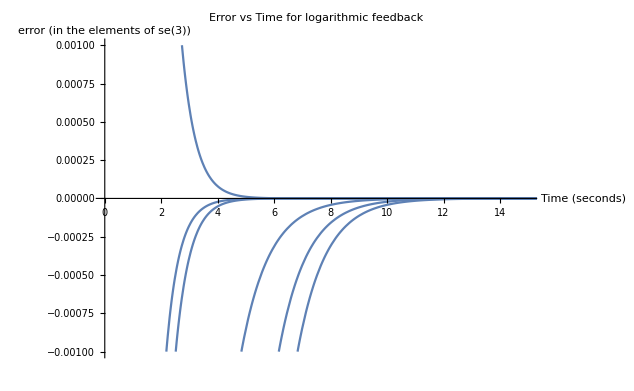

```mathematica
Plot[(z[t]/.logerror), {t, 0, 50}, PlotRange->{{0, 15}, {-0.001, 0.001}}, AxesLabel->{"Time (seconds) ", "error (in the elements of se(3))"} , PlotLabel->"Error vs Time for logarithmic feedback"]
```

```mathematica
(*Finding the values of the actual elements*)
```

```mathematica
R62dual[z_]:=Module[{},
Return[{z[[1;;3]],z[[4;;6]]}];
]
```

```mathematica
R62dual[z[t]/.logerror/.t->0.1]
```

{{-0.836423,-0.11435,-0.430302},{0.176134,-0.131414,-0.07189}}

```mathematica
(*This solves the regulation problem using se3*)
```

```mathematica
(*Now to see the differences in the path taken by both these methods we need to plot the end-effector location and orientation*)
```

```mathematica
(*So we need to start making a visualisation module*)
```

```mathematica
(*/.Point[a___]:>{Thick,Line[a]}*)
```

```mathematica
logdq[N[fkq/.sampleangles]/.params]
logdq[N[fkq/.sampleangles3]/.params]
```

{{-2.63132,0.470235,-0.953744},{0.0651801,0.153568,0.0241239}}

{{-1.55384,-0.0793013,-0.912813},{-0.00287481,-0.0855135,-0.105936}}

```mathematica
fkm1 = fkq/.params/.Table[Inner[Rule, θsym, ((z[t]/.motionsim)/.t->tval)[[1;;6]], List],{tval, 0, 15, 0.005}];
```

```mathematica
fkm1//Dimensions
```

{3001,2,2}

```mathematica
config2 = Table[Flatten[logdq[fkm1[[i]]]], {i, 3001}];
```

```mathematica
(*To visualise the complete motion we need a marker axes which moves with the end-effector*)
```

```mathematica
(*Verifying the properties of logarithm for dual quaternions*)
```

```mathematica
tempei = dqmult[cdualq[qd2], qi]
```

{{0.5,{-0.764464,-0.104512,-0.393283}},{0.113152,{0.163245,0.059,-0.18914}}}

```mathematica
Chop[dqmult[qd2, tempei]-qi]
```

{{0,{0,0,0}},{0,{0,0,0}}}

```mathematica
logdq[tempei]
```

{{-0.92439,-0.126376,-0.475558},{0.211094,-0.167466,-0.0781114}}

```mathematica
logdq[cdualq[qd2]]+logdq[qi]
```

{{-1.07748,0.549537,-0.0409313},{0.177564,0.122519,-0.046226}}

```mathematica
(*Not the same!*)
```

```mathematica
logdq[dqmult[qd2, tempei]]
```

{{-2.63132,0.470235,-0.953744},{0.0651801,0.153568,0.0241239}}

```mathematica
logdq[qi]
```

{{-2.63132,0.470235,-0.953744},{0.0651801,0.153568,0.0241239}}

```mathematica
(*Hence the normal logarithmic identities do not work for dual quaternions as the multiplication here has different rules*)
```

```mathematica
explogdq[logdq_]:=Module[{tempθ, tempk},
tempθ = Norm[logdq[[1]]];
tempk = logdq[[1]]/tempθ;
Return[unitdq[2*logdq[[2]], 2*tempθ, tempk]];
];
```

```mathematica
Chop[dqmult[qd2, explogdq[logdq[ei]]]-qi]
```

{{0,{0,0,0}},{0,{0,0,0}}}

```mathematica
logdq[dqmult[qd2,explogdq[R62dual[z[t]/.logerror/.t->0]]]]
```

{{-2.63132,0.470235,-0.953744},{0.0651801,0.153568,0.0241239}}

```mathematica
config = Table[Flatten[logdq[dqmult[qd2,explogdq[R62dual[z[t]/.logerror/.t->tval]]]]],{tval, 0, 15, 0.005}];
```

```mathematica
config//Dimensions
```

{3001,6}

```mathematica
(*PlotRange->{{-1,-0.4},{0,1},{-3, 3}}*)
```

```mathematica
(*Though interpreting these plots doesnt make sense, we can see that in the second case i.e. in config2 case, the change in the angles and the axis is very small compared to the other case*)
```

```mathematica
logdq[qi][[2]]
logdq[qd2][[2]]
(logdq[qi][[2]]-logdq[qd2][[2]])*2
```

{0.0651801,0.153568,0.0241239}

{-0.00287481,-0.0855135,-0.105936}

{0.13611,0.478164,0.260119}

```mathematica
config[[1]]
config2[[1]]
config[[-1]]
config2[[-1]]
```

{-2.63132,0.470235,-0.953744,0.0651801,0.153568,0.0241239}

{-2.63132,0.470235,-0.953744,0.0651801,0.153568,0.0241239}

{-1.55385,-0.0793013,-0.912813,-0.00287481,-0.0855135,-0.105936}

{-1.55384,-0.0793013,-0.912813,-0.00287487,-0.0855136,-0.105936}

```mathematica
(*We can see from below, that if planned using the wrong controller the end-effector moves in a curved path and has some overshoot which may not be desired. Also the motion is rapid initially for the wrong control case and the controller takes huge cartesian steps per iteration*)
```

```mathematica
Show[ListPointPlot3D[2*config[[;;,4;;6]], PlotStyle->{Red}], ListPointPlot3D[2*config2[[;;,4;;6]], PlotStyle->{Blue}], PlotRange->{{-0.5, 0.5}, {-0.2, 0.3}, {-0.8, 0.8}}]
```

-Graphics3D-

```mathematica
(*Plotting a coordinate axis in space*)
```

```mathematica
f1 = Show[Graphics3D[{Blue, Arrow[{{0,0,0},{0,0,1}}]}], Graphics3D[{Green, Arrow[{{0,0,0},{0,1,0}}]}], Graphics3D[{Red, Arrow[{{0,0,0},{1,0,0}}]}]];
f2 = Show[Graphics3D[{Blue, Arrow[{{1,1,1},{1,1,2}}]}], Graphics3D[{Green, Arrow[{{1,1,1},{1,2,1}}]}], Graphics3D[{Red, Arrow[{{1,1,1},{2,1,1}}]}]];
f3 = Show[Graphics3D[{Blue, Arrow[{{0,0,0},{0,-1/(√2),1/(√2)}}]}], Graphics3D[{Green, Arrow[{{0,0,0},{0,1/(√2),1/(√2)}}]}], Graphics3D[{Red, Arrow[{{0,0,0},{1,0,0}}]}]];
```

```mathematica
Show[f1, f2, f3];
```

```mathematica
(*Plots the frame given the log of a dual quaternion or the se(3) element*)
```

```mathematica
frameplotter[logdq_]:=Module[{θvec, θval, kvec, Amat, Rmat, tvec, origin, l, point, r},
(*l is the length of the axis that needs to be plotted and the radius of the point*)
l = 0.2;
r = 0.01;
(*Show[Graphics3D[{Blue, Arrow[{{0,0,0},{0,0,1}}]}], Graphics3D[{Green, Arrow[{{0,0,0},{0,1,0}}]}], Graphics3D[{Red, Arrow[{{0,0,0},{1,0,0}}]}]]*)
θvec = 2*logdq[[1;;3]];
tvec = 2*logdq[[4;;6]];
θval = Norm[θvec];
kvec = θvec/θval;
(*Using the Rodrigues formulation for finding the rotation matrix. So formulating the Rodrigues parameters*)
Amat = vec2SkewMat[kvec*Tan[θval/2]];
Rmat = (Inverse[IdentityMatrix[3]-Amat].(IdentityMatrix[3]+Amat));
(*Plots z, y, x, axis respectively*)
origin = Show[Graphics3D[{Black, Sphere[{0,0,0}, r]}],Graphics3D[{Blue, Arrow[{{0,0,0},{0,0,l}}]}], Graphics3D[{Green, Arrow[{{0,0,0},{0,l,0}}]}], Graphics3D[{Red, Arrow[{{0,0,0},{l,0,0}}]}]];
(*We also need to mark the coordinate to which the frame is attached*)
point = Graphics3D[{Black, Sphere[tvec,r]}];
(*Returning the transformed frame and the origin*)
Return[Show[origin, Graphics3D[{Blue, Arrow[{tvec,tvec+Rmat.{0,0,l}}]}], Graphics3D[{Green, Arrow[{tvec,tvec+Rmat.{0,l,0}}]}], Graphics3D[{Red, Arrow[{tvec,tvec+Rmat.{l,0,0}}]}], point]];
]
```

```mathematica
(*The end-effector orientation for the two control schemes*)
```

```mathematica
Show[Table[frameplotter[2*config2[[i]]], {i, 301}]];
```

```mathematica
Show[Table[frameplotter[2*config[[i]]], {i, 301}]];
```

```mathematica
Manipulate[Show[Table[frameplotter[2*config2[[i]]], {i, j}]],{j, 1, 301}];
```

```mathematica
Manipulate[Show[Table[frameplotter[2*config[[i]]], {i, j}]],{j, 1, 301}];
```

```mathematica
zeefangdc = Table[2*(logdq[fkqp/.zθrule[[i]]]), {i, 10001}];
```

```mathematica
(*This brings a closure to the comparison between the L2 norm based controller and the logratihmic controller*)
```

```mathematica
(*Trying to show the motion one frame at a time*)
```

```mathematica
Manipulate[Show[frameplotter[2*config2[[1]]], frameplotter[2*config2[[300]]], frameplotter[2*config2[[i]]]],{i, 1, 300, 1}];
```

```mathematica
Manipulate[Show[frameplotter[2*config[[1]]], frameplotter[2*config[[300]]], frameplotter[2*config[[i]]]],{i, 1, 300, 1}];
```

```mathematica
(*Closer investigation of the seeming discontinuity in the beginning of the L2 controller*)
```

```mathematica
Manipulate[Show[frameplotter[Flatten[zeefangdc[[1]]]], frameplotter[Flatten[zeefangdc[[-1]]]], frameplotter[Flatten[zeefangdc[[i]]]]],{i, 1, 1001, 1}];
```

```mathematica
Manipulate[Show[frameplotter[Flatten[zeefangdc[[1]]]], frameplotter[Flatten[zeefangdc[[-1]]]],Table[frameplotter[Flatten[zeefangdc[[i]]]], {i, j}]],{j, 1, 1001, 1}];
```

```mathematica
(*Now showing both the controllers togethers, one frame at a time*)
```

```mathematica
Manipulate[Show[frameplotter[2*config[[1]]], frameplotter[2*config[[-1]]], frameplotter[2*config[[i]]],frameplotter[2*config2[[1]]], frameplotter[2*config2[[-1]]], frameplotter[2*config2[[i]]]],{i, 1, 600, 1}];
```

```mathematica
(*Manipulation trying to show the trajectory and the path in one plot, using frames for time histories*)
```

```mathematica
Manipulate[Show[frameplotter[2*config2[[-1]]], Table[frameplotter[2*config2[[i]]], {i, j}]],{j, 1, 401, 1}];
```

```mathematica
Manipulate[Show[frameplotter[2*config[[-1]]], Table[frameplotter[2*config[[i]]], {i, j}]],{j, 1, 401, 1}];
```

```mathematica
(*Investigation based on the gains of the *)
```